# GPU-VH Code Tests

## Setup

### working directory

```mathematica
wd=SetDirectory@NotebookDirectory[]
root=ParentDirectory[wd]
```

/home/bazow/mercury/gpu-vh/mathematica

/home/bazow/mercury/gpu-vh

### constants

```mathematica
hbarc=0.197326938;
```

```mathematica
Nc=3;
Nf=2.5;
fac=3(2(Nc^2-1)+7/2Nc*Nf)Pi^2/90;
facT=fac^(1/4);
```

### plot styles

```mathematica
styles={Directive[RGBColor[0,0,0],AbsoluteThickness[4]],Directive[RGBColor[0.9,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]],Directive[RGBColor[0,0,0.5],AbsoluteThickness[3],AbsoluteDashing[{10,5}]],Directive[RGBColor[0,0.5,0],AbsoluteThickness[3],AbsoluteDashing[{10,5,2,5}]],Directive[RGBColor[1,0.5,0.0],AbsoluteThickness[3],AbsoluteDashing[{1,4}]],Directive[RGBColor[0.5,0.5,0.5],AbsoluteThickness[2],AbsoluteDashing[{1,4}]]};
```

```mathematica
FrameTicksFontSize=20;
FrameFontSize=20;PlotOptions={Axes->False,Frame->True,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]]},AspectRatio->0.75,ImageSize->600,PlotStyle->styles,PlotRange->All};
SetOptions[Plot,PlotOptions];
SetOptions[LogPlot,PlotOptions];
SetOptions[LogLogPlot,PlotOptions];
SetOptions[LogLinearPlot,PlotOptions];
SetOptions[ListPlot,PlotOptions];
SetOptions[PolarPlot,PlotOptions];
```

### data reader

```mathematica
Off[Interpolation::inhr];
varInt[t_,dir_,var_]:=Interpolation[Import[dir<>"/"<>var<>"_"<>ToString[PaddedForm[t,{4,3},NumberPadding->{"","0"}]]<>".dat"],InterpolationOrder->3]
```

## Conformal generalized Isreal-Stewart Bjorken

```mathematica
tlist=Table[t,{t,0.25,20.25,.05}];
```

### semi-analytical solution

```mathematica
Clear[t,t0,tf,etabar,temp,T0,T,gamma,betapi,e0,p,teq,beta,pi,pi0,teqVH,gamma2,eiso,piso]
```

```mathematica
t0=0.25;
tf=20;
```

```mathematica
etabar=0.2;
```

```mathematica
T0=3.05;
```

```mathematica
beta=38/21;
```

```mathematica
temp[e_]=(e/fac)^(1/4);
```

```mathematica
teq[e_]=5*etabar/temp[e];
```

```mathematica
gamma=1;
eiso[T_]=fac*T^4;
piso[T_]=eiso[T]/3;
```

```mathematica
p[e_]=e/3;
```

```mathematica
betapi[e_]=4p[e]/5;
```

```mathematica
e0=eiso[T0];
```

```mathematica
pi0=2/(3*t0)*etabar*(eiso[T0]+piso[T0])/T0;
```

```mathematica
{eExact,piExact}={e,pi}/.NDSolve[{D[e[t],t]==-(e[t]+p[e[t]]-pi[t])/t,D[pi[t],t]==-pi[t]/teq[e[t]]+betapi[e[t]](4/3/t)-beta*pi[t]/t,e[t0]==e0,pi[t0]==pi0},{e,pi},{t,t0,tf}][[1]];
```

### load gpu-vh numerical data

```mathematica
outputDir=root<>"/test/bjorken/conformal";
```

```mathematica
lim=-Import[outputDir<>"/e_"<>ToString[PaddedForm[tlist[[1]],{4,3},NumberPadding->{"","0"}]]<>".dat"][[1,1]];
```

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed⟦1,1⟧ is longer than depth of object.

```mathematica
Clear[eInt,pinnInt]
```

```mathematica
MapThread[Table[#1[i-1]=varInt[tlist[[i]],outputDir,#2],{i,1,Length[tlist]}]&,{{eInt,pinnInt},{"e","pinn"}}];
```

```mathematica
ectr=Interpolation[Table[{tlist[[i]],eInt[i-1][0,0,0]},{i,1,Length[tlist]}],InterpolationOrder->3];
pinnctr=Interpolation[Table[{tlist[[i]],pinnInt[i-1][0,0,0]},{i,1,Length[tlist]}],InterpolationOrder->3];
```

### make plots

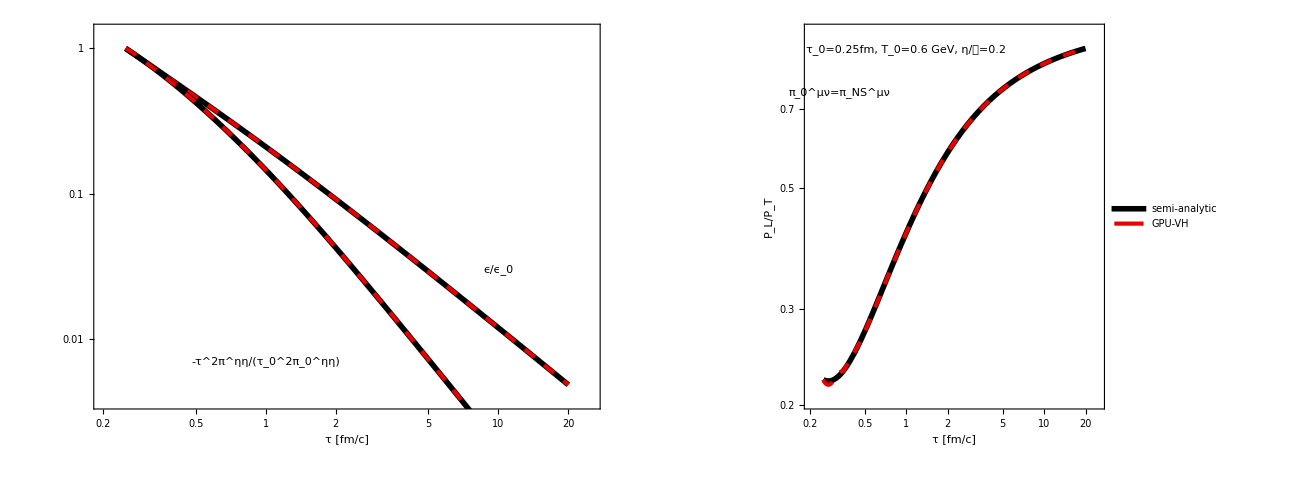

```mathematica
p1=Show[LogLogPlot[{eExact[t]/eExact[.25],ectr[t]/ectr[.25]},{t,t0,tf},PlotRange->All],LogLogPlot[{piExact[t]/pi0,-t^2pinnctr[t]/pi0},{t,t0,tf},PlotRange->All],FrameLabel->{"τ [fm/c]",""},ImageSize->600,Epilog->{Inset["ϵ/ϵ_0",{Log[10],Log[.03]},BaseStyle->{FontFamily->"Times",FontSize->30}],Inset["-τ^2π^ηη/(τ_0^2π_0^ηη)",{Log[1],Log[.007]},BaseStyle->{FontFamily->"Times",FontSize->30}]}];
p2=LogLogPlot[{(p[eExact[t]]-piExact[t])/(p[eExact[t]]+piExact[t]/2),(ectr[t]/3+t^2pinnctr[t])/(ectr[t]/3-t^2pinnctr[t]/2)},{t,t0,tf},PlotRange->All,FrameLabel->{"τ [fm/c]","P_L/P_T"},ImageSize->600,PlotLegends->Placed[LineLegend[styles,{"semi-analytic","GPU-VH"},LabelStyle-> {FontSize->20},LegendMarkerSize->{{100,20}}],{.7,0.2}],Epilog->{Inset["τ_0="<>ToString[t0]<>"fm, T_0=0.6 GeV, η/𝒮=0.2",{Log[1],Log[.9]},BaseStyle->{FontFamily->"Times",FontSize->20}],Inset["π_0^μν=π_NS^μν",{Log[.33],Log[.75]},BaseStyle->{FontFamily->"Times",FontSize->20}]}];
conformalBjorkenPlot=GraphicsGrid[{{p1,p2}}]
```

```mathematica
Export[wd<>"/conformalBjorkenPlot.pdf",conformalBjorkenPlot]
```

/home/bazow/mercury/gpu-vh/mathematica/conformalBjorkenPlot.pdf

## Nonconformal generalized Isreal-Stewart Bjorken

```mathematica
tlist=Table[t,{t,0.25,5.25,.05}];
```

### semi-analytical solution

#### EoS

```mathematica
eosDir ="/rhic/rhic-trunk/src/main/resources/eos/wuppertal-budapest/";
```

```mathematica
eosDataRaw=Import[ParentDirectory[wd]<>eosDir<>"eos.dat"];
eosData= Take[eosDataRaw,{3,Length[eosDataRaw]}];
LogEDLogTInt = Interpolation[eosData[[All,{1,2}]]];
edInt[T_] = 10^LogEDLogTInt[Log[10,T]];
LogPLogTInt = Interpolation[eosData[[All,{1,4}]]];
PInt[T_] = 10^LogPLogTInt[Log[10,T]];
```

```mathematica
LogdPLogTInt = Interpolation[eosData[[All,{1,5}]]];
dPInt[T_] = 10^LogdPLogTInt[Log[10,T]];
LogdELogTInt = Interpolation[eosData[[All,{1,3}]]];
dEInt[T_] = 10^LogdELogTInt[Log[10,T]];
```

#### parameters

```mathematica
t0=0.25;
tf=20;
```

```mathematica
etabar=0.2;
```

```mathematica
T0=3.05;
```

```mathematica
e0=edInt[T0];
```

```mathematica
pi0=2/(3*t0)*etabar*(edInt[T0]+PInt[T0])/T0;
```

```mathematica
Pi0=0;
```

```mathematica
zetabar[T_]:=Module[{A1,A2,A3,lambda1,lambda2,lambda3,lambda4,sigma1,sigma2,sigma3,sigma4,x},
A1=-13.77;
A2=27.55;
A3=13.45;
lambda1=0.9;
lambda2=0.25;
lambda3=0.9;
lambda4=0.22;
sigma1=0.025;
sigma2=0.13;
sigma3=0.0025;
sigma4=0.022;
x=T/1.01355;
If[x>1.05,Return[lambda1*Exp[-(x-1)/sigma1]+lambda2*Exp[-(x-1)/sigma2]+0.001]];
If[x<0.995,Return[lambda3*Exp[(x-1)/sigma3]+lambda4*Exp[(x-1)/sigma4]+0.03]];
Return[A1*x*x+A2*x-A3];
];
```

#### bulk viscous pressure transport coefficients

```mathematica
betaPi[T_]:=15(1/3-dPInt[T]/dEInt[T])^2(edInt[T]+PInt[T])
```

```mathematica
lambdaPipi[T_]:=8(1/3-dPInt[T]/dEInt[T])/5
```

```mathematica
tauPiInv[T_]:=15(1/3-dPInt[T]/dEInt[T])^2T/zetabar[T]
```

```mathematica
deltaPiPi=0.666667;
```

#### shear stress tensor transport coefficients

```mathematica
taupiInv[T_]:=T/5/etabar;
```

```mathematica
deltapipi=1.33333;
```

```mathematica
taupipi=1.42857;
```

```mathematica
lambdapiPi=1.2;
```

#### equations

```mathematica
Clear[e,pi,pizz,TExact,piExact,pizzExact]
```

```mathematica
eqs={D[edInt[T[t]],t]==-(edInt[T[t]]+PInt[T[t]]+pi[t]-pizz[t])/t,D[pi[t],t]==-pi[t]tauPiInv[T[t]]-betaPi[T[t]]/t-deltaPiPi*pi[t]/t+lambdaPipi[T[t]]pizz[t]/t,D[pizz[t],t]==-pizz[t]taupiInv[T[t]]+4betapi[T[t]]/(3t)-(taupipi/3+deltapipi)*pizz[t]/t+2*lambdapiPi*pi[t]/(3t)};
initcond={T[t0]==T0,pi[t0]==0,pizz[t0]==pi0};
{TExact,piExact,pizzExact}={T,pi,pizz}/.NDSolve[Join[eqs,initcond],{T,pi,pizz},{t,t0,20}][[1]];
```

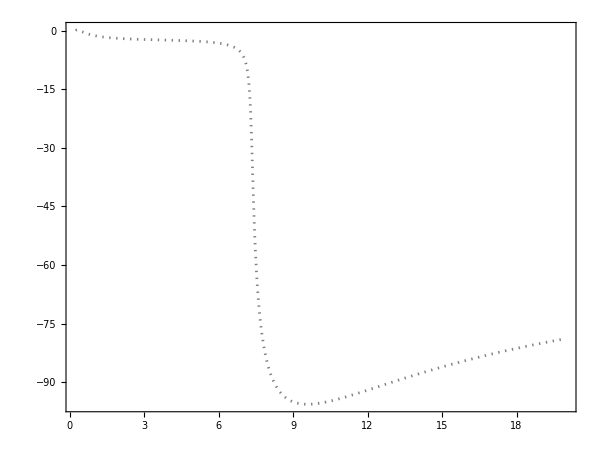

```mathematica
Plot[piExact[t],{t,t0,tf}]
```

### load gpu-vh numerical data

```mathematica
outputDir=root<>"/test/bjorken/nonconformal";
```

```mathematica
lim=-Import[outputDir<>"/e_"<>ToString[PaddedForm[tlist[[1]],{4,3},NumberPadding->{"","0"}]]<>".dat"][[1,1]];
```

```mathematica
Clear[eInt,PiInt,pinnInt]
```

```mathematica
MapThread[Table[#1[i-1]=varInt[tlist[[i]],outputDir,#2],{i,1,Length[tlist]}]&,{{eInt,PiInt,pinnInt},{"e","Pi","pinn"}}];
```

$Aborted

```mathematica
MapThread[Table[#1[i-1]=varInt[tlist[[i]],outputDir,#2],{i,1,Length[tlist]}]&,{{eInt},{"e"}}];
```

```mathematica
ectr=Interpolation[Table[{tlist[[i]],eInt[i-1][0,0,0]},{i,1,Length[tlist]}],InterpolationOrder->3];
Pictr=Interpolation[Table[{tlist[[i]],PiInt[i-1][0,0,0]},{i,1,Length[tlist]}],InterpolationOrder->3];
pinnctr=Interpolation[Table[{tlist[[i]],pinnInt[i-1][0,0,0]},{i,1,Length[tlist]}],InterpolationOrder->3];
```

```mathematica
ectr=Interpolation[Table[{tlist[[i]],eInt[i-1][0,0,0]},{i,1,Length[tlist]}],InterpolationOrder->3];
```

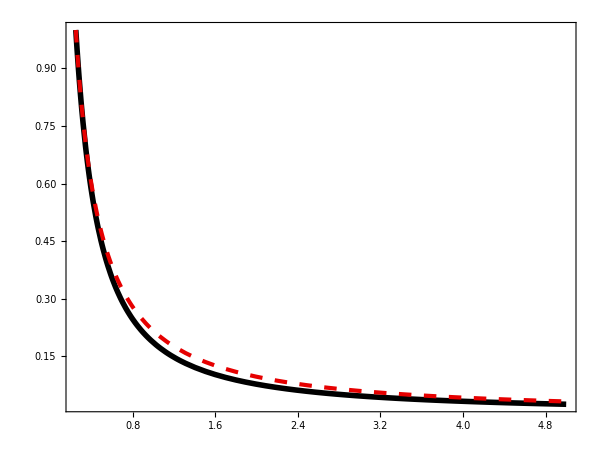

```mathematica
Plot[{edInt[TExact[t]]/edInt[TExact[.25]],ectr[t]/ectr[.25]},{t,t0,5},PlotRange->All]
```

## Nonconformal generalized Isreal-Stewart Bjorken--energy density

```mathematica
tlist=Table[t,{t,0.25,20.25,.05}];
```

### semi-analytical solution

#### EoS

```mathematica
LogPLogEd[x_]:=(-6118.240942492361-5687.251105195098 x+20752.76275644727 x^2-11989.517475674438 x^3+6431.189740977292 x^4-1887.7892172219235 x^5+5662.745060345452 x^6+774.6684795499582 x^7+1583.4830157257804 x^8+564.4875398887923 x^9+72.61447772796548 x^10-3.708800297832573 x^11-2.1867927513752687 x^12-0.08312033181718484 x^13+0.04120042172447292 x^14+0.006603398115960931 x^15+0.0006175106780064349 x^16+0.00006482843976373467 x^17+4.770229269047069*^-6 x^18+9.71339211307907*^-8 x^19-2.6695366906807306*^-9 x^20+2.2395809810298253*^-10 x^21+1.0976424753178406*^-11 x^22-4.0048841416263433*^-13 x^23)/(7543.6556170684635+15151.776822013266 x-8032.374892077859 x^2+9482.306880935743 x^3+3014.631292911099 x^4+6373.655296404095 x^5+1545.3557368707916 x^6+1844.8983613169753 x^7+611.425805536374 x^8+71.10312213702488 x^9-5.337616978647186 x^10-2.219457520808683 x^11-0.049308529548886815 x^12+0.04431464626883895 x^13+0.006751646144424717 x^14+0.0006534305815342522 x^15+0.00006835809883063034 x^16+4.7788306567603985*^-6 x^17+9.073105345833764*^-8 x^18-2.375015494438446*^-9 x^19+2.384121844661416*^-10 x^20+1.0397720666824917*^-11 x^21-4.00498303992117*^-13 x^22-1.3258095394882071*^-20 x^23)
```

```mathematica
P[e_]=10^(LogPLogEd[Log[10,e]]);
```

```mathematica
cs2[e_]:=(1.2625814949136498*^-42+2.4439030393295734*^-33 e+9.322641344497548*^-26 e^2+1.9540661873302495*^-19 e^3+5.0244280894342345*^-14 e^4+2.369176131226614*^-9 e^5+0.00002467595835925649 e^6+0.0608709022174928 e^7+35.13582886022962 e^8+4222.887394189519 e^9+72483.09074617726 e^10+417317.67297479673 e^11+585334.4710663276 e^12+57539.2198687339 e^13+14441.972045822631 e^14+1216.0067118006687 e^15+13.489236656837132 e^16+14.786577881305382 e^17-2.5565796031645758 e^18+0.05603218920634199 e^19+0.000984102224155054 e^20+2.1161830800816893*^-6 e^21+8.101199742688298*^-10 e^22+3.89552175647867*^-14 e^23)/(3.56558833745313*^-41+4.6403916630291216*^-32 e+1.246926715508643*^-24 e^2+1.9406804331642527*^-18 e^3+3.8792079821435393*^-13 e^4+1.473941085930358*^-8 e^5+0.0001283715493908053 e^6+0.27578987407916083 e^7+144.29417387657588 e^8+16436.520976883963 e^9+315466.19533599314 e^10+2.8901807318940037*^6 e^11+5.506960426273549*^6 e^12-355776.5733809447 e^13+156209.84678369848 e^14-5701.991686556281 e^15+832.8660760210314 e^16+1.9784144986425583 e^17-7.706332342730179 e^18+0.20216864185984038 e^19+0.00313721024057907 e^20+6.541440626577012*^-6 e^21+2.4689937881750025*^-9 e^22+1.1758507795621395*^-13 e^23)
```

```mathematica
Tint[e_]:=(-4.873400811469563*^-10-0.33967898165285937 e-243.87315076666465 e^2-7950.4417656525575 e^3-15830.731725359203 e^4-1638.2165592489832 e^5-15.708990537469983 e^6-0.017506852476184522 e^7-1.836593645164133*^-6 e^8)/(-4.873378567876981*^-6-1.9735695129421675 e-691.5144322242182 e^2-13185.130839434429 e^3-20098.669864541644 e^4-1169.8522357611525 e^5-6.630649855145946 e^6-0.004312673981317225 e^7-2.1655522622011757*^-7 e^8)
```

```mathematica
ed[T_]:=(-0.011958188410851651+119.89423098138208 T-3156.9475699248055 T^2+32732.86844374939 T^3-187899.8994764422 T^4+712537.3610845465 T^5-1.557049803609345*^6 T^6+1.4852519861308339*^6 T^7+532132.6079941876 T^8-1.963099445042592*^6 T^9-4484.44579242679 T^10+1.7984228830058286*^6 T^11+119345.25619517374 T^12-1.3499773937058165*^6 T^13-207838.4995663606 T^14+654970.2138652403 T^15-78643.00334616247 T^16+40274.00078068926 T^17+422619.58977657766 T^18-409688.07836393174 T^19-62005.75915066359 T^20+46788.14270090656 T^21+40784.330477857235 T^22-12589.47744840392 T^23)/(31630.074365558292-127100.88940643385 T+173528.1225422275 T^2-39403.297956865215 T^3-85582.57873541754 T^4+9320.560804233442 T^5+50882.74198960172 T^6+20335.926473421183 T^7-14897.725710713818 T^8-23836.484117457 T^9-13726.013896090335 T^10+4517.908673107615 T^11+18056.19917986404 T^12+14954.82860467155 T^13+2569.623976952738 T^14-9304.046211514986 T^15-15606.429173842751 T^16+8383.710735812094 T^17+1591.3177623932843 T^18-678.748230997762 T^19-33.58687934953277 T^20+3.2520554133126285 T^21-0.19647288043440464 T^22+0.005443394551264717 T^23)
```

#### parameters

```mathematica
t0=0.25;
tf=20;
```

```mathematica
etabar=0.2;
```

```mathematica
T0=3.05;
```

```mathematica
e0=ed[T0];
```

```mathematica
pizz0=2/(3*t0)*etabar*(e0+P[e0])/T0;
```

```mathematica
pizz0
```

255.086

```mathematica
{t0,etabar,e0,P[e0],T0}
```

{0.25,0.2,1111.04,347.734,3.05}

```mathematica
Pi0=0;
```

```mathematica
zetabar[e_]:=Module[{A1,A2,A3,lambda1,lambda2,lambda3,lambda4,sigma1,sigma2,sigma3,sigma4,x,res},
A1=-13.77;
A2=27.55;
A3=13.45;
lambda1=0.9;
lambda2=0.25;
lambda3=0.9;
lambda4=0.22;
sigma1=0.025;
sigma2=0.13;
sigma3=0.0025;
sigma4=0.022;
x=Tint[e]/1.01355;
If[x>1.05,Return[lambda1*Exp[-(x-1)/sigma1]+lambda2*Exp[-(x-1)/sigma2]+0.001]];
If[x<0.995,Return[lambda3*Exp[(x-1)/sigma3]+lambda4*Exp[(x-1)/sigma4]+0.03]];
Return[A1*x*x+A2*x-A3];
];
```

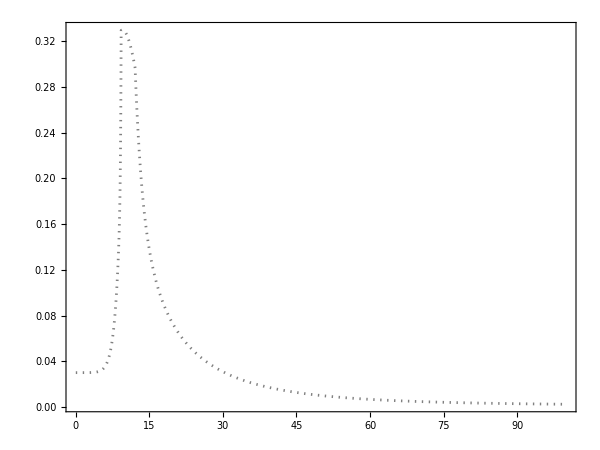

```mathematica
Plot[zetabar[e],{e,0.001,100}]
```

#### bulk viscous pressure transport coefficients

```mathematica
betaPi[e_]:=15(1/3-cs2[e])^2(e+P[e])
```

```mathematica
lambdaPipi[e_]:=8(1/3-cs2[e])/5
```

```mathematica
tauPiInv[e_]:=15(1/3-cs2[e])^2Tint[e]/zetabar[e]
```

```mathematica
deltaPiPi=0.666667;
```

#### shear stress tensor transport coefficients

```mathematica
betapi[e_]:=(e+P[e])/5
```

```mathematica
taupiInv[e_]:=Tint[e]/5/etabar;
```

```mathematica
deltapipi=1.33333;
```

```mathematica
taupipi=1.42857;
```

```mathematica
lambdapiPi=1.2;
```

```mathematica
{taupipi,deltapipi,lambdapiPi,deltaPiPi}
```

{1.42857,1.33333,1.2,0.666667}

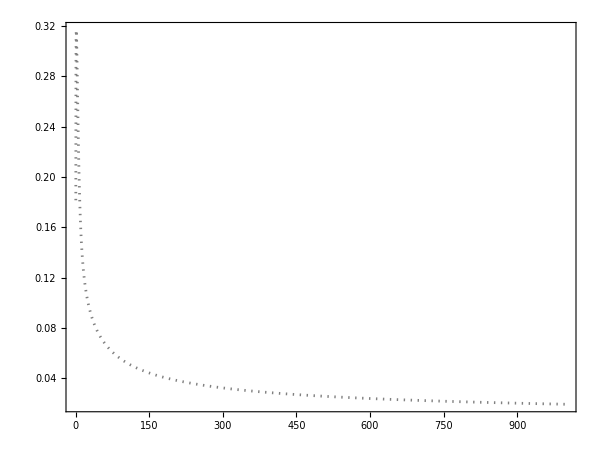

```mathematica
Plot[lambdaPipi[e],{e,0.001,1000}]
```

#### equations

```mathematica
Clear[e,pi,pizz,edExact,piExact,pizzExact]
```

```mathematica
eqs={D[e[t],t]==-(e[t]+P[e[t]]+pi[t]-pizz[t])/t,D[pi[t],t]==-pi[t]tauPiInv[e[t]]-betaPi[e[t]]/t-deltaPiPi*pi[t]/t+lambdaPipi[e[t]]pizz[t]/t,D[pizz[t],t]==-pizz[t]taupiInv[e[t]]+betapi[e[t]](4/3/t)-(taupipi/3+deltapipi)*pizz[t]/t+2*lambdapiPi*pi[t]/3/t};
initcond={e[t0]==e0,pi[t0]==0,pizz[t0]==pizz0};
{edExact,piExact,pizzExact}={e,pi,pizz}/.NDSolve[Join[eqs,initcond],{e,pi,pizz},{t,t0,20}][[1]];
```

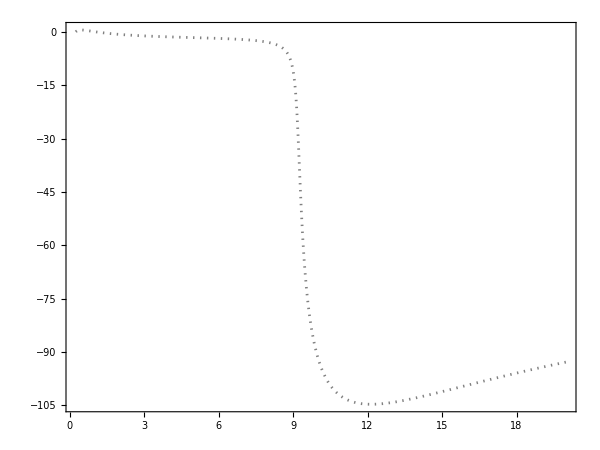

```mathematica
Plot[{piExact[t]},{t,t0,tf},PlotRange->All]
```

### load gpu-vh numerical data

```mathematica
outputDir=root<>"/test/bjorken/nonconformal";
```

```mathematica
lim=-Import[outputDir<>"/e_"<>ToString[PaddedForm[tlist[[1]],{4,3},NumberPadding->{"","0"}]]<>".dat"][[1,1]];
```

```mathematica
Clear[eInt,PiInt,pinnInt]
```

```mathematica
MapThread[Table[#1[i-1]=varInt[tlist[[i]],outputDir,#2],{i,1,Length[tlist]}]&,{{eInt,PiInt,pinnInt},{"e","Pi","pinn"}}];
```

```mathematica
ectr=Interpolation[Table[{tlist[[i]],eInt[i-1][0,0,0]},{i,1,Length[tlist]}],InterpolationOrder->3];
Pictr=Interpolation[Table[{tlist[[i]],PiInt[i-1][0,0,0]},{i,1,Length[tlist]}],InterpolationOrder->3];
pinnctr=Interpolation[Table[{tlist[[i]],pinnInt[i-1][0,0,0]},{i,1,Length[tlist]}],InterpolationOrder->3];
```

```mathematica
edExact=Interpolation[Import["/home/bazow/Documents/bjorken/nonconformal/ed.dat"]];
PiExact=Interpolation[Import["/home/bazow/Documents/bjorken/nonconformal/Pi.dat"]];
pizzExact=Interpolation[Import["/home/bazow/Documents/bjorken/nonconformal/pizz.dat"]];
```

```mathematica
t0=.25;
```

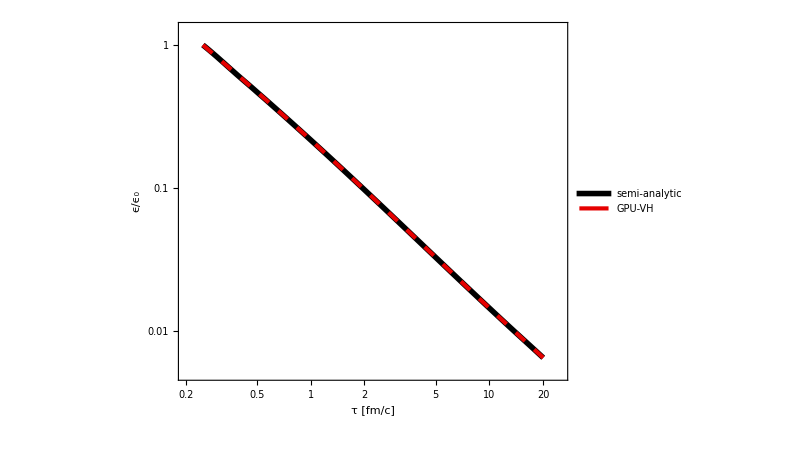

```mathematica
edPlot=LogLogPlot[{edExact[t]/edExact[t0],ectr[t]/ectr[t0]},{t,t0,20},PlotRange->All,PlotRange->All,FrameLabel->{"τ [fm/c]","ϵ/ϵ_0"},ImageSize->600,PlotLegends->Placed[LineLegend[styles,{"semi-analytic","GPU-VH"},LabelStyle-> {FontSize->20},LegendMarkerSize->{{100,20}}],{.7,0.8}]]
```

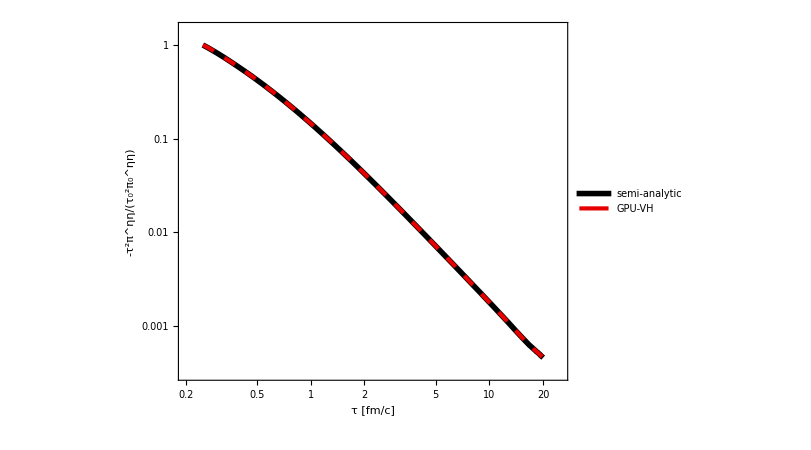

```mathematica
pinnPlot=LogLogPlot[{pizzExact[t]/pizzExact[t0],(t/t0)^2pinnctr[t]/pinnctr[t0]},{t,t0,20},PlotRange->All,PlotRange->All,FrameLabel->{"τ [fm/c]","-τ^2π^ηη/(τ_0^2π_0^ηη)"},ImageSize->600,PlotLegends->Placed[LineLegend[styles,{"semi-analytic","GPU-VH"},LabelStyle-> {FontSize->20},LegendMarkerSize->{{100,20}}],{.7,0.8}]]
```

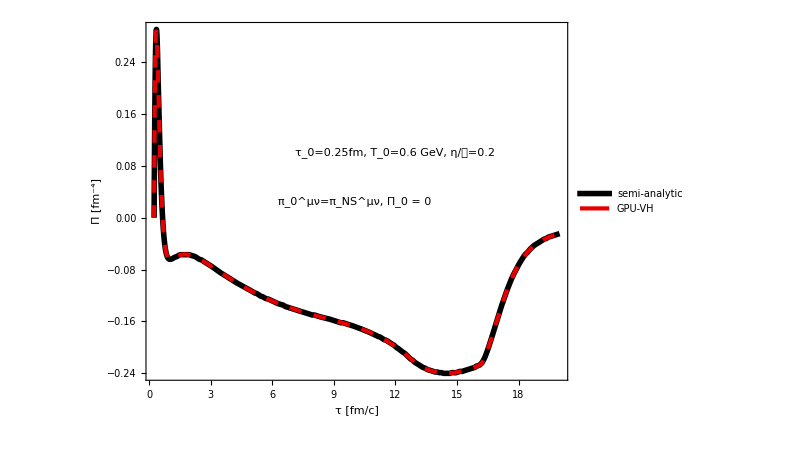

```mathematica
PiPlot=Plot[{PiExact[t],Pictr[t]},{t,t0,20},FrameLabel->{"τ [fm/c]","Π [fm^-4]"},ImageSize->600,PlotLegends->Placed[LineLegend[styles,{"semi-analytic","GPU-VH"},LabelStyle-> {FontSize->20},LegendMarkerSize->{{100,20}}],{.7,0.8}],Epilog->{Inset["τ_0="<>ToString[t0]<>"fm, T_0=0.6 GeV, η/𝒮=0.2",{12,.1},BaseStyle->{FontFamily->"Times",FontSize->20}],Inset["π_0^μν=π_NS^μν, Π_0 = 0",{10,0.025},BaseStyle->{FontFamily->"Times",FontSize->20}]}]
```

```mathematica
Export[wd<>"/nonconformalBjorkenPlot_ed.pdf",edPlot]
Export[wd<>"/nonconformalBjorkenPlot_pinn.pdf",pinnPlot]
Export[wd<>"/nonconformalBjorkenPlot_Pi.pdf",PiPlot]
```

/home/bazow/mercury/gpu-vh/mathematica/nonconformalBjorkenPlot_ed.pdf

/home/bazow/mercury/gpu-vh/mathematica/nonconformalBjorkenPlot_pinn.pdf

/home/bazow/mercury/gpu-vh/mathematica/nonconformalBjorkenPlot_Pi.pdf

## Ideal Gubser

```mathematica
tlist={1.5,2,3};
```

### analytical solution

```mathematica
ux[t_,x_,y_,{q_}]:=x*Sinh[ArcTanh[2q t q Sqrt[x^2+y^2]/(1+q^2t^2+q^2(x^2+y^2))]]/Sqrt[x^2+y^2]
```

```mathematica
temp[t_,r_,{T0_,q_}]:=T0(2q*t)^(2/3)/(t(1+2q^2(t^2+r^2)+q^4(t^2-r^2)^2)^(1/3))
```

```mathematica
temp2[t_,x_,y_,{T0_,q_}]:=T0(2q*t)^(2/3)/(t(1+2q^2(t^2+x^2+y^2)+q^4(t^2-x^2-y^2)^2)^(1/3))
```

### load gpu-vh numerical data

```mathematica
outputDir=root<>"/test/gubser/ideal";
```

```mathematica
lim=-Import[outputDir<>"/e_"<>ToString[PaddedForm[tlist[[1]],{3,3},NumberPadding->{"","0"}]]<>".dat"][[1,1]];
```

```mathematica
Clear[eInt,uxInt]
```

```mathematica
MapThread[Table[#1[i-1]=varInt[tlist[[i]],#2],{i,1,Length[tlist]}]&,{{eInt,uxInt},{"e","ux"}}];
```

### make plots

```mathematica
edPlot=Show[Table[Plot[{fac*temp2[tlist[[i]],x,0,{1.2,1}]^4+(Length[tlist]-i)*0.5,eInt[i-1][x,0,0]+(Length[tlist]-i)*0.5},{x,-lim,lim}],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","ϵ[fm^-4]"},ImageSize->600];
```

```mathematica
uxPlot=Show[Plot[{ux[tlist[[1]],x,0,{1}],uxInt[0][x,0,0]},{x,-lim,lim},PlotLegends->Placed[LineLegend[styles,{"analytic","GPU-VH"},LabelStyle-> {FontSize->20},LegendMarkerSize->{{100,20}}],{.7,0.3}]],Table[Plot[{ux[tlist[[i]],x,0,{1}],uxInt[i-1][x,0,0]},{x,-lim,lim}],{i,2,Length[tlist]}],FrameLabel->{"x [fm]","u^x"},ImageSize->600,Epilog->Inset["τ_0="<>ToString[1]<>"fm, T_0=1.2 fm^-1",{-1.5,3},BaseStyle->{FontFamily->"Times",FontSize->20}]];
```

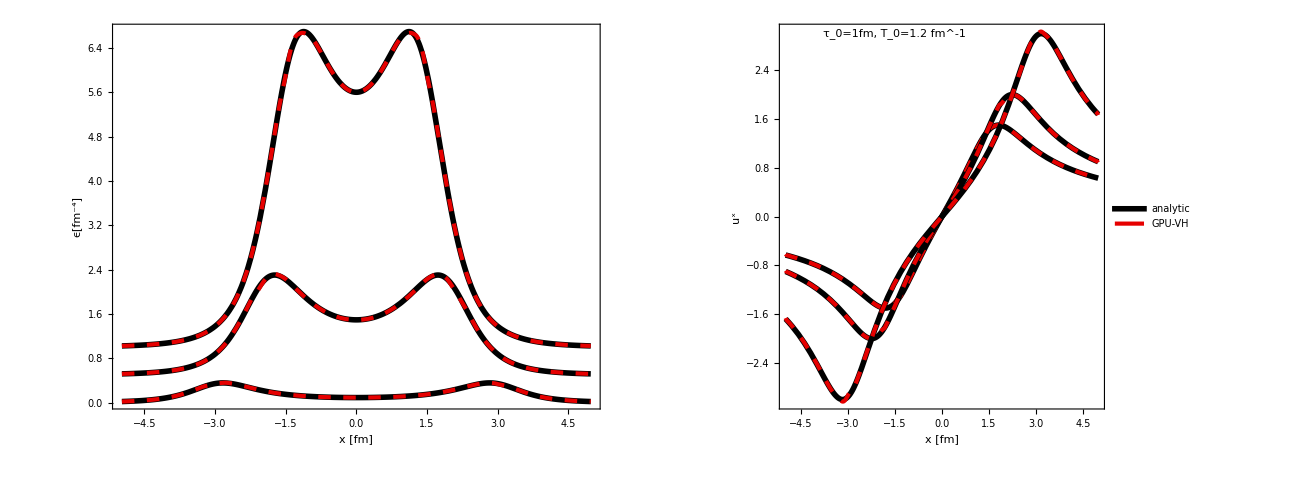

```mathematica
edUxGridIdeal=GraphicsGrid[{{edPlot,uxPlot}}]
```

```mathematica
Export[wd<>"/edUxGridIdeal.pdf",edUxGridIdeal]
```

/home/bazow/mercury/gpu-vh/mathematica/edUxGridIdeal.pdf

## Isreal-Stewart Gubser

```mathematica
tlist={1.5,2,3};
```

### semi-analytical solution

```mathematica
etaS=0.2;
{Tsol,pisol}={T,pi}/.NDSolve[{T'[p]==-2T[p]/3*Tanh[p]-T[p]/3*pi[p]*Tanh[p],pi'[p]+T[p]pi[p]/(5*etaS)-4*pi[p]^2*Tanh[p]/3==-4*Tanh[p]/15,T[0]==1.2,pi[0]==0},{T,pi},{p,-10,10}][[1]];
Tm[t_,r_]:=facT*Tsol[ArcSinh[-(1-t^2+r^2)/2/t]]/t
em[t_,r_]:=Tm[t,r]^4
pi[t_,r_]:=4*(em[t,r]/3)*pisol[ArcSinh[-(1-t^2+r^2)/2/t]]
```

```mathematica
ux[t_,x_,y_,{q_}]:=x*Sinh[ArcTanh[2*q*t*q*Sqrt[x^2+y^2]/(1+q^2*t^2+q^2(x^2+y^2))]]/Sqrt[x^2+y^2]
```

### load gpu-vh numerical data

```mathematica
outputDir=root<>"/test/gubser/viscous";
```

```mathematica
lim=-Import[outputDir<>"/e_"<>ToString[PaddedForm[tlist[[1]],{3,3},NumberPadding->{"","0"}]]<>".dat"][[1,1]];
```

```mathematica
Clear[eInt,uxInt,pinnInt]
```

```mathematica
MapThread[Table[#1[i-1]=varInt[tlist[[i]],outputDir,#2],{i,1,Length[tlist]}]&,{{eInt,uxInt,pinnInt},{"e","ux","pinn"}}];
```

### make plots

```mathematica
edPlot=Show[Table[Plot[{em[tlist[[i]],x]+(Length[tlist]-i)*0.5,eInt[i-1][x,0,0]+(Length[tlist]-i)*0.5},{x,-lim,lim}],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","ϵ[fm^-4]"},ImageSize->600];
```

```mathematica
uxPlot=Show[Plot[{ux[tlist[[1]],x,0,{1}],uxInt[0][x,0,0]},{x,-lim,lim},PlotLegends->Placed[LineLegend[styles,{"semi-analytic","GPU-VH"},LabelStyle-> {FontSize->20},LegendMarkerSize->{{100,20}}],{.7,0.3}]],Table[Plot[{ux[tlist[[i]],x,0,{1}],uxInt[i-1][x,0,0]},{x,-lim,lim}],{i,2,Length[tlist]}],FrameLabel->{"x [fm]","u^x"},ImageSize->600,Epilog->Inset["τ_0="<>ToString[1]<>"fm, T_0=1.2 fm^-1, η/𝒮=0.2",{-1.5,3},BaseStyle->{FontFamily->"Times",FontSize->20}]];
```

```mathematica
pinnPlot=Show[Table[Plot[{-pi[tlist[[i]],x],(tlist[[i]])^2pinnInt[i-1][x,0,0]},{x,-lim,lim}],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","τ^2π^ηη [fm^-4]"},ImageSize->600];
```

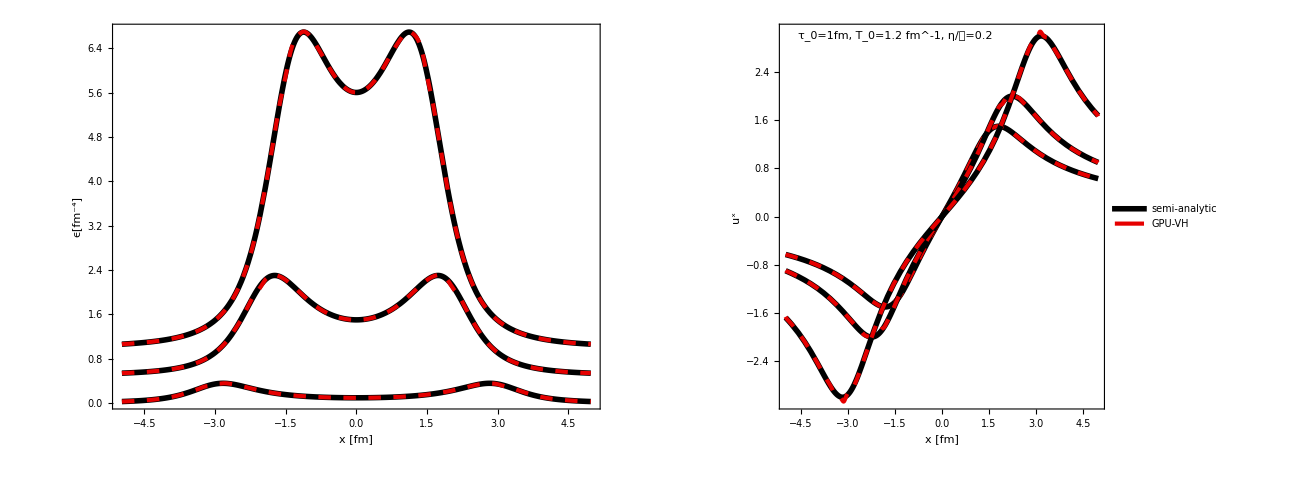

```mathematica
edUxGrid=GraphicsGrid[{{edPlot,uxPlot}}]
```

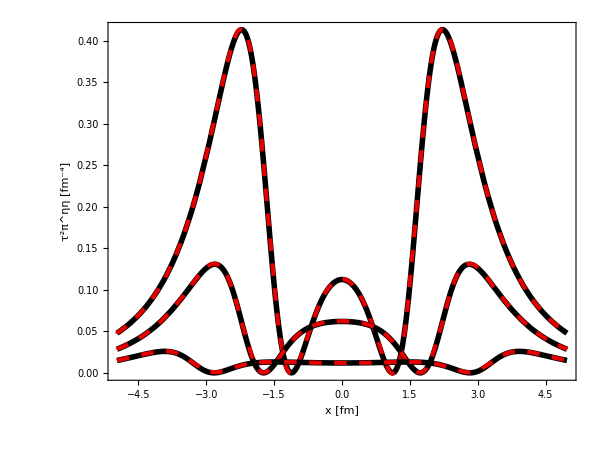

```mathematica
Show[pinnPlot]
```

```mathematica
Export[wd<>"/ePlot.pdf",edPlot]
Export[wd<>"/uxPlot.pdf",uxPlot]
Export[wd<>"/pinnPlot.pdf",pinnPlot]
Export[wd<>"/edUxGrid.pdf",edUxGrid]
```

/home/bazow/mercury/gpu-vh/mathematica/ePlot.pdf

/home/bazow/mercury/gpu-vh/mathematica/uxPlot.pdf

/home/bazow/mercury/gpu-vh/mathematica/pinnPlot.pdf

/home/bazow/mercury/gpu-vh/mathematica/edUxGrid.pdf

## Relativistic Sod shock-tube

```mathematica
tlist={4};
```

### load gpu-vh numerical data

```mathematica
sodDir=root<>"/test/riemann/sod";
```

```mathematica
Clear[eInt,uxInt,utInt]
```

#### analytic result (dx=0.005 fm and \theta=1)

```mathematica
outputDir=sodDir<>"/analytic";
lim=-Import[outputDir<>"/e_"<>ToString[PaddedForm[tlist[[1]],{3,3},NumberPadding->{"","0"}]]<>".dat"][[1,1]];
MapThread[Table[#1[i-1]=varInt[tlist[[i]],outputDir,#2],{i,1,Length[tlist]}]&,{{eInt,uxInt,utInt},{"e","ux","ut"}}];
```

#### change dx with flux limiter \theta=1 constant

```mathematica
outputDir=sodDir<>"/dx/0p1";
MapThread[Table[#1[i-1]=varInt[tlist[[i]],outputDir,#2],{i,1,Length[tlist]}]&,{{eInt0p1,uxInt0p1,utInt0p1},{"e","ux","ut"}}];
```

```mathematica
outputDir=sodDir<>"/dx/0p05";
MapThread[Table[#1[i-1]=varInt[tlist[[i]],outputDir,#2],{i,1,Length[tlist]}]&,{{eInt0p05,uxInt0p05,utInt0p05},{"e","ux","ut"}}];
```

```mathematica
outputDir=sodDir<>"/dx/0p025";
MapThread[Table[#1[i-1]=varInt[tlist[[i]],outputDir,#2],{i,1,Length[tlist]}]&,{{eInt0p025,uxInt0p025,utInt0p025},{"e","ux","ut"}}];
```

```mathematica
outputDir=sodDir<>"/dx/0p01";
MapThread[Table[#1[i-1]=varInt[tlist[[i]],outputDir,#2],{i,1,Length[tlist]}]&,{{eInt0p01,uxInt0p01,utInt0p01},{"e","ux","ut"}}];
```

#### change flux limiter \theta with dx=0.1 fm constant

```mathematica
outputDir=sodDir<>"/theta/1";
MapThread[Table[#1[i-1]=varInt[tlist[[i]],outputDir,#2],{i,1,Length[tlist]}]&,{{eInt1,uxInt1,utInt1},{"e","ux","ut"}}];
```

```mathematica
outputDir=sodDir<>"/theta/1p5";
MapThread[Table[#1[i-1]=varInt[tlist[[i]],outputDir,#2],{i,1,Length[tlist]}]&,{{eInt1p5,uxInt1p5,utInt1p5},{"e","ux","ut"}}];
```

```mathematica
outputDir=sodDir<>"/theta/1p8";
MapThread[Table[#1[i-1]=varInt[tlist[[i]],outputDir,#2],{i,1,Length[tlist]}]&,{{eInt1p8,uxInt1p8,utInt1p8},{"e","ux","ut"}}];
```

```mathematica
outputDir=sodDir<>"/theta/2";
MapThread[Table[#1[i-1]=varInt[tlist[[i]],outputDir,#2],{i,1,Length[tlist]}]&,{{eInt2,uxInt2,utInt2},{"e","ux","ut"}}];
```

### make plots

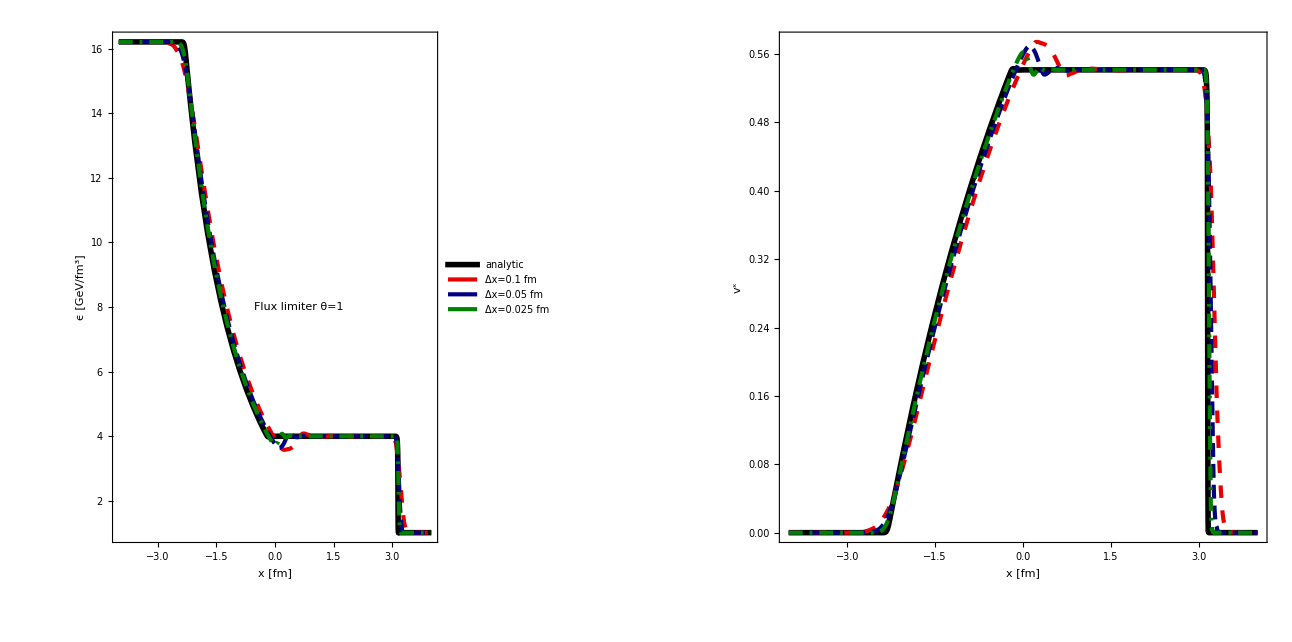

```mathematica
edPlot=Show[Table[Plot[{eInt[i-1][x,0,0]/hbarc^3,eInt0p1[i-1][x,0,0]/hbarc^3,eInt0p05[i-1][x,0,0]/hbarc^3,eInt0p025[i-1][x,0,0]/hbarc^3},{x,-lim,lim},PlotLegends->Placed[LineLegend[styles,{"analytic","Δx=0.1 fm","Δx=0.05 fm","Δx=0.025 fm"},LabelStyle-> {FontSize->20},LegendMarkerSize->{{100,20}}],{.65,0.7}]],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","ϵ [GeV/fm^3]"},Epilog->Inset["Flux limiter θ=1",{0.6,8},BaseStyle->{FontFamily->"Times",FontSize->20}],ImageSize->600];
uxPlot=Show[Table[Plot[{uxInt[i-1][x,0,0]/utInt[i-1][x,0,0],uxInt0p1[i-1][x,0,0]/utInt0p1[i-1][x,0,0],uxInt0p05[i-1][x,0,0]/utInt0p05[i-1][x,0,0],uxInt0p025[i-1][x,0,0]/utInt0p025[i-1][x,0,0]},{x,-lim,lim}],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","v^x"},ImageSize->600];
sodGridDeltaX=GraphicsGrid[{{edPlot,uxPlot}}]
```

```mathematica
Export[wd<>"/sodGridDeltaX.pdf",sodGridDeltaX]
```

/home/bazow/mercury/gpu-vh/mathematica/sodGridDeltaX.pdf

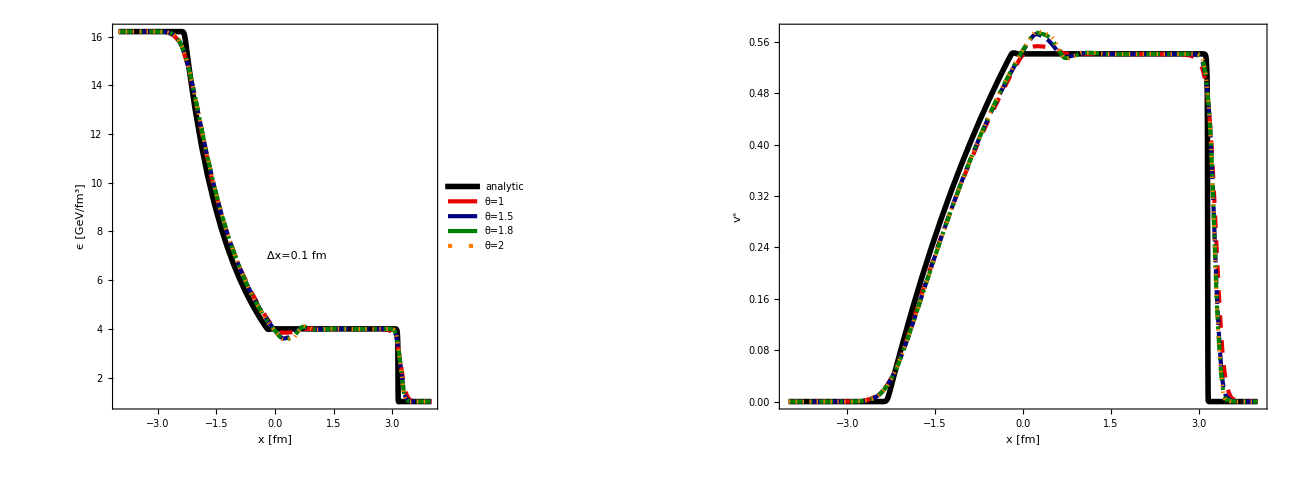

```mathematica
edPlot=Show[Table[Plot[{eInt[i-1][x,0,0]/hbarc^3,eInt1[i-1][x,0,0]/hbarc^3,eInt1p5[i-1][x,0,0]/hbarc^3,eInt1p8[i-1][x,0,0]/hbarc^3,eInt2[i-1][x,0,0]/hbarc^3},{x,-lim,lim},PlotLegends->Placed[LineLegend[styles,{"analytic","θ=1","θ=1.5","θ=1.8","θ=2"},LabelStyle-> {FontSize->20},LegendMarkerSize->{{100,20}}],{.65,0.7}]],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","ϵ [GeV/fm^3]"},Epilog->Inset["Δx=0.1 fm",{0.55,7},BaseStyle->{FontFamily->"Times",FontSize->20}],ImageSize->600];
uxPlot=Show[Table[Plot[{uxInt[i-1][x,0,0]/utInt[i-1][x,0,0],uxInt1[i-1][x,0,0]/utInt1[i-1][x,0,0],uxInt1p5[i-1][x,0,0]/utInt1p5[i-1][x,0,0],uxInt1p8[i-1][x,0,0]/utInt1p8[i-1][x,0,0],uxInt2[i-1][x,0,0]/utInt2[i-1][x,0,0]},{x,-lim,lim}],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","v^x"},ImageSize->600];
sodGridTheta=GraphicsGrid[{{edPlot,uxPlot}}]
```

```mathematica
Export[wd<>"/sodGridTheta.pdf",sodGridTheta]
```

/home/bazow/mercury/gpu-vh/mathematica/sodGridTheta.pdf

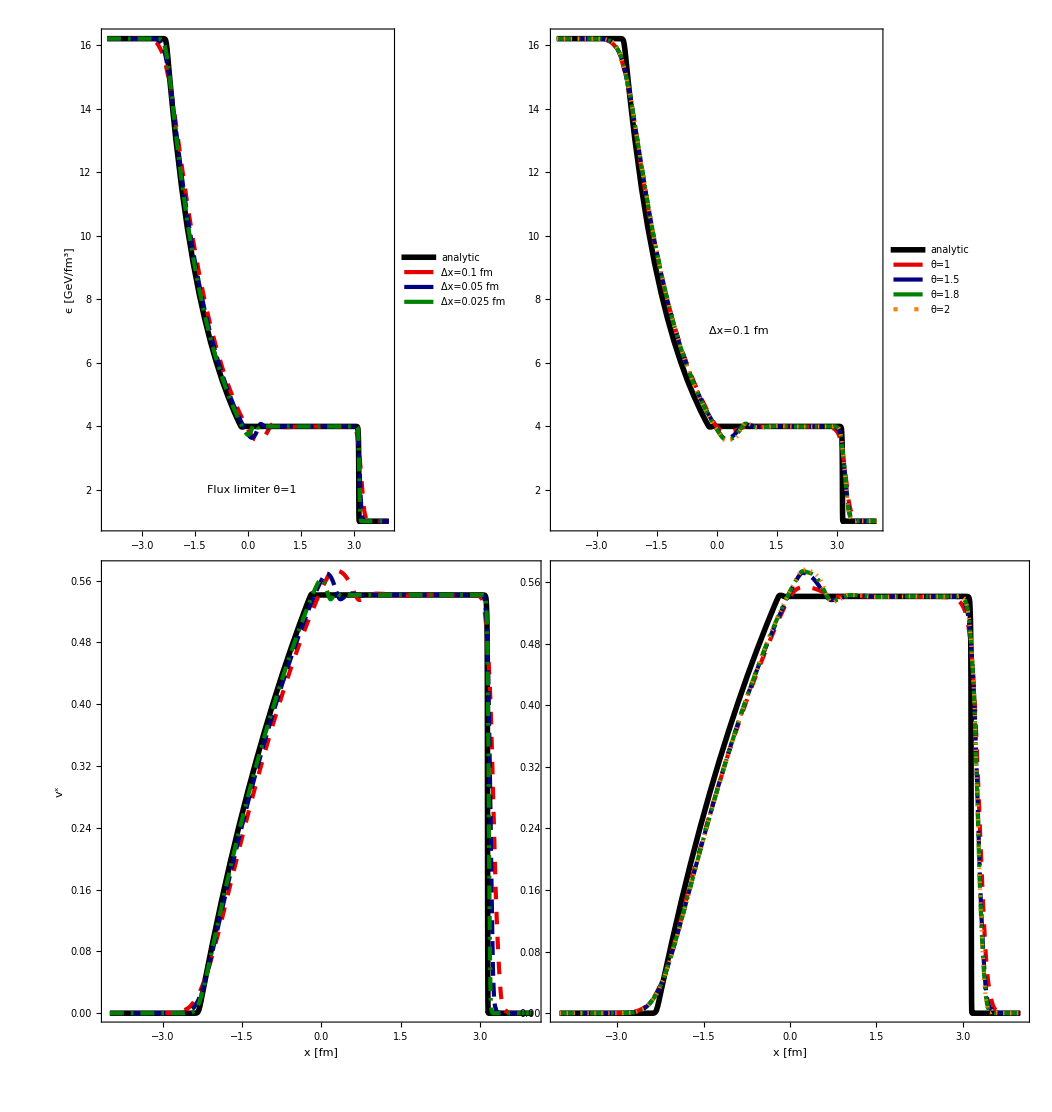

```mathematica
edPlot1=Show[Table[Plot[{eInt[i-1][x,0,0]/hbarc^3,eInt0p1[i-1][x,0,0]/hbarc^3,eInt0p05[i-1][x,0,0]/hbarc^3,eInt0p025[i-1][x,0,0]/hbarc^3},{x,-lim,lim},PlotLegends->Placed[LineLegend[styles,{"analytic","Δx=0.1 fm","Δx=0.05 fm","Δx=0.025 fm"},LabelStyle-> {FontSize->20},LegendMarkerSize->{{100,20}}],{.65,0.7}]],{i,1,Length[tlist]}],FrameLabel->{"","ϵ [GeV/fm^3]"},Epilog->Inset["Flux limiter θ=1",{0.1,2},BaseStyle->{FontFamily->"Times",FontSize->20}],ImagePadding->{{100,30},{80,50}}];
uxPlot1=Show[Table[Plot[{uxInt[i-1][x,0,0]/utInt[i-1][x,0,0],uxInt0p1[i-1][x,0,0]/utInt0p1[i-1][x,0,0],uxInt0p05[i-1][x,0,0]/utInt0p05[i-1][x,0,0],uxInt0p025[i-1][x,0,0]/utInt0p025[i-1][x,0,0]},{x,-lim,lim}],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","v^x"},ImageSize->600,ImagePadding->{{100,30},{80,50}}];
edPlot2=Show[Table[Plot[{eInt[i-1][x,0,0]/hbarc^3,eInt1[i-1][x,0,0]/hbarc^3,eInt1p5[i-1][x,0,0]/hbarc^3,eInt1p8[i-1][x,0,0]/hbarc^3,eInt2[i-1][x,0,0]/hbarc^3},{x,-lim,lim},PlotLegends->Placed[LineLegend[styles,{"analytic","θ=1","θ=1.5","θ=1.8","θ=2"},LabelStyle-> {FontSize->20},LegendMarkerSize->{{100,20}}],{.65,0.7}]],{i,1,Length[tlist]}],Epilog->Inset["Δx=0.1 fm",{0.55,7},BaseStyle->{FontFamily->"Times",FontSize->20}],ImagePadding->{{100,30},{80,50}}];
uxPlot2=Show[Table[Plot[{uxInt[i-1][x,0,0]/utInt[i-1][x,0,0],uxInt1[i-1][x,0,0]/utInt1[i-1][x,0,0],uxInt1p5[i-1][x,0,0]/utInt1p5[i-1][x,0,0],uxInt1p8[i-1][x,0,0]/utInt1p8[i-1][x,0,0],uxInt2[i-1][x,0,0]/utInt2[i-1][x,0,0]},{x,-lim,lim}],{i,1,Length[tlist]}],FrameLabel->{"x [fm]",""},ImagePadding->{{100,30},{80,50}}];
sodGrid=GraphicsGrid[{{edPlot1,edPlot2},{uxPlot1,uxPlot2}},Spacings->{-80, -50}]
```

```mathematica
Export[wd<>"/sodGrid.pdf",sodGrid]
```

/home/bazow/mercury/gpu-vh/mathematica/sodGrid.pdf

## Additional Riemann problems

## Implosion in a box

```mathematica
tlist={0,2,4,8};
```

```mathematica
tlist={0};
```

```mathematica
tlist=Table[t,{t,0,1,.05}];
```

```mathematica
tlist={0,.5};
```

```mathematica
outputDir=root<>"/test/riemann/implosion";
```

```mathematica
lim=-Import[outputDir<>"/e_"<>ToString[PaddedForm[tlist[[1]],{3,3},NumberPadding->{"","0"}]]<>".dat"][[1,1]];
```

```mathematica
Clear[eInt]
```

```mathematica
MapThread[Table[#1[i-1]=varInt[tlist[[i]],outputDir,#2],{i,1,Length[tlist]}]&,{{eInt},{"e"}}];
```

```mathematica
jet[u_?NumericQ]:=Blend[{{0,RGBColor[0,0,9/16]},{1/9,Blue},{23/63,Cyan},{13/21,Yellow},{47/63,Orange},{55/63,Red},{1,RGBColor[1/2,0,0]}},u]/;0≤u≤1
```

```mathematica
max=Max[Table[eInt[0][x,y,0],{x,0,lim,0.01},{y,0,lim,.01}]]
```

0.0171201

```mathematica
dataRaw=Import[outputDir<>"/e_"<>ToString[PaddedForm[tlist[[2]],{3,3},NumberPadding->{"","0"}]]<>".dat"];
```

```mathematica
data=Table[dataRaw[[i+201*(j-1)]][[4]],{i,1,201},{j,1,201}];
```

```mathematica
Length[data[[1]]]
```

201

```mathematica
ListContourPlot[data,ColorFunction->jet,Contours->Automatic,ImageSize->600,Frame->True,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]]},AspectRatio->1,FrameLabel->{"x [fm]","y [fm]"},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->600,LegendMargins->{{10,0},{0,-30}},LabelStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]]}],Right]]
```

-Graphics-

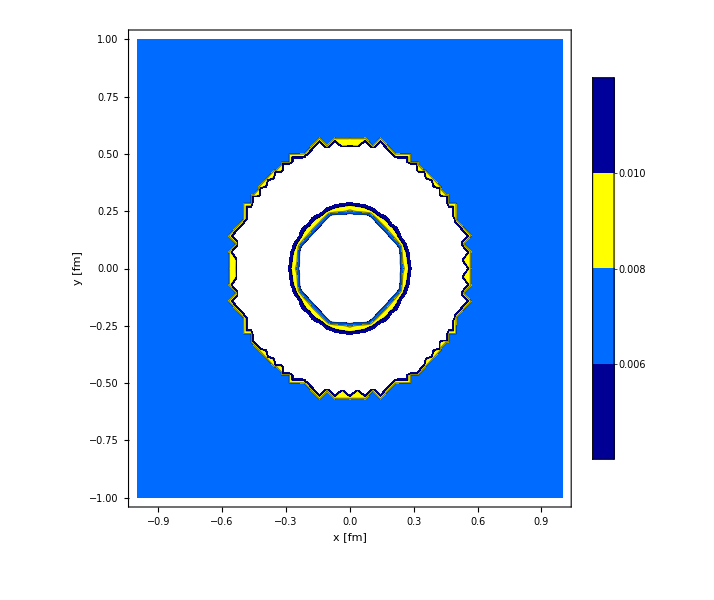

```mathematica
ContourPlot[eInt[1][x,y,0],{x,-lim,lim},{y,-lim,lim},ColorFunction->jet,Contours->Automatic,ImageSize->600,Frame->True,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]]},AspectRatio->1,FrameLabel->{"x [fm]","y [fm]"},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->600,LegendMargins->{{10,0},{0,-30}},LabelStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]]}],Right]]
```

```mathematica
2*1/0.01+1
```

201.

## Rayleigh-Taylor instibility

```mathematica
tlist={1};
```

```mathematica
root="/home/bazow/mercury/gpu-vh/output";
```

```mathematica
Off[Interpolation::inhr];
varInt[t_,var_]:=Interpolation[Import[outputDir<>"/"<>var<>"_"<>ToString[PaddedForm[t,{3,3},NumberPadding->{"","0"}]]<>".dat"],InterpolationOrder->3]
```

```mathematica
lim=-Import[outputDir<>"/e_"<>ToString[PaddedForm[tlist[[1]],{3,3},NumberPadding->{"","0"}]]<>".dat"][[1,1]];
```

```mathematica
Clear[eInt,uxInt,utInt]
```

```mathematica
outputDir=root;
MapThread[Table[#1[i-1]=varInt[tlist[[i]],#2],{i,1,Length[tlist]}]&,{{eInt,uxInt,utInt},{"e","ux","ut"}}];
```

```mathematica
ContourPlot[eInt[0][x,y,0],{x,-.2,.2},{y,-.2,.2},ColorFunction->jet,Contours->101,ImageSize->600,Frame->True,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]]},AspectRatio->1,FrameLabel->{"x [fm]","y [fm]"},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->600,LegendMargins->{{10,0},{0,-30}},LabelStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]]}],Right]]
```

-Graphics-

```mathematica
Solve[(nx-1)/2*d==a,nx]
```

{{nx→(2 a+d)/d}}

```mathematica
2*(1/6)/0.1+1
```

4.33333

## Rayleigh-Taylor instibility

```mathematica
tlist=Table[t,{t,0,1,0.05}];
```

```mathematica
tlist={1,2};
```

```mathematica
root="/home/bazow/mercury/gpu-vh/output";
```

```mathematica
Off[Interpolation::inhr];
varInt[t_,var_]:=Interpolation[Import[outputDir<>"/"<>var<>"_"<>ToString[PaddedForm[t,{3,3},NumberPadding->{"","0"}]]<>".dat"],InterpolationOrder->3]
```

```mathematica
lim=-Import[outputDir<>"/e_"<>ToString[PaddedForm[tlist[[1]],{3,3},NumberPadding->{"","0"}]]<>".dat"][[1,1]];
```

```mathematica
Import[outputDir<>"/e_"<>ToString[PaddedForm[tlist[[1]],{3,3},NumberPadding->{"","0"}]]<>".dat"]
```

{{-1.,-1.,-0.025,2.5},{-0.99,-1.,-0.025,2.5},{-0.98,-1.,-0.025,2.5},{-0.97,-1.,-0.025,2.5},{-0.96,-1.,-0.025,2.5},{-0.95,-1.,-0.025,2.5},{-0.94,-1.,-0.025,2.5},{-0.93,-1.,-0.025,2.5},{-0.92,-1.,-0.025,2.5},{-0.91,-1.,-0.025,2.5},80782,{0.91,1.,0.025,2.5},{0.92,1.,0.025,2.5},{0.93,1.,0.025,2.5},{0.94,1.,0.025,2.5},{0.95,1.,0.025,2.5},{0.96,1.,0.025,2.5},{0.97,1.,0.025,2.5},{0.98,1.,0.025,2.5},{0.99,1.,0.025,2.5},{1.,1.,0.025,2.5}}
 |  |  |  |

```mathematica
Clear[eInt,uxInt,utInt]
```

```mathematica
outputDir=root;
MapThread[Table[#1[i-1]=varInt[tlist[[i]],#2],{i,1,Length[tlist]}]&,{{eInt,tttInt,ttnInt},{"e","ttt","ttn"}}];
```

```mathematica
tttInt[0]
```

InterpolatingFunction[{{-1., 1.}, {-1., 1.}, {-0.025, 0.025}}, <>]

```mathematica
Etot[i_]:=tlist[[i]]*NIntegrate[(Cosh[n]tttInt[i-1][x,y,n]+tlist[[i-1]]*Sinh[n]*ttnInt[0][x,y,n]),{x,-lim,lim},{y,-lim,lim},{n,-0.025,0.025}]
```

```mathematica
Etot[2]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.35946 and 0.0000539443 for the integral and error estimates.

3.35946

```mathematica
Clear[et]
```

```mathematica
et=Interpolation[Table[{tlist[[i]],eInt[i][0,0,0]},{i,1,Length[tlist]}],InterpolationOrder->3]
```

InterpolatingFunction[{{0., 1.}}, <>]

```mathematica
eg[x_,y_]:=(1+0.1*Exp[-50*((x-0.5)^2+(y-0.5)^2)])/(1.4-1);
```

```mathematica
etest[x_,y_]:=eInt[Length[tlist]-1][x,y,0]-eg[x,y]
```

```mathematica
etest[0,0]
```

1.5

```mathematica
Length[tlist]
```

21

```mathematica
NIntegrate[eInt[2][x,y,0],{x,-lim,lim},{y,-lim,lim},MaxRecursion->20,Method->{GlobalAdaptive,MaxErrorIncreases->10000}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

10.203

```mathematica
totalEdExact=NIntegrate[eg[x,y],{x,-lim,lim},{y,-lim,lim}]
```

10.0157

```mathematica
Table[NIntegrate[eInt[i-1][x,y,0],{x,-lim,lim},{y,-lim,lim},MaxRecursion->20,Method->{GlobalAdaptive,MaxErrorIncreases->10000}]-totalEdExact,{i,1,Length[tlist]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 11.111 and 0.000011223 for the integral and error estimates.

$Aborted

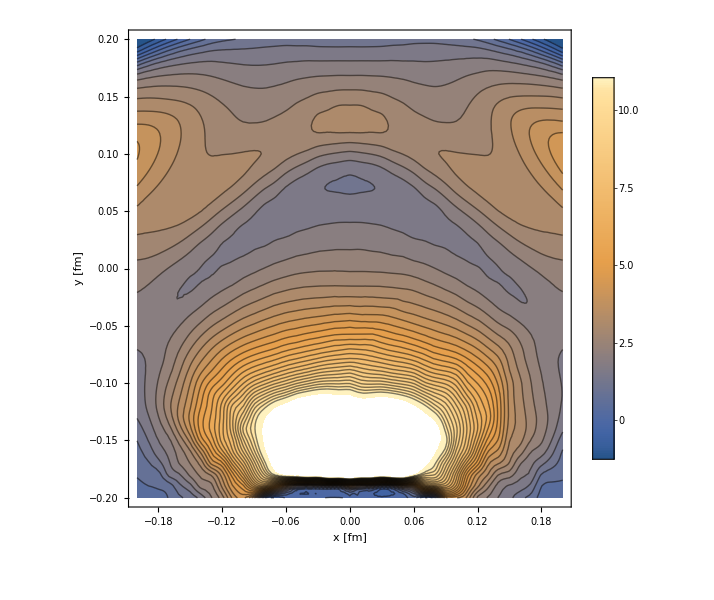

```mathematica
ContourPlot[(etest[x,y]),{x,-.2,.2},{y,-.2,.2},Contours->31,ImageSize->600,Frame->True,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]]},AspectRatio->1,FrameLabel->{"x [fm]","y [fm]"},PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->600,LegendMargins->{{10,0},{0,-30}},LabelStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]]}],Right]]
```

```mathematica
Solve[(nx-1)/2*d==a,nx]
```

{{nx→(2 a+d)/d}}

```mathematica
2*(1/6)/0.1+1
```

4.33333

## Energy conservation

```mathematica
tlist={0.5,1};
```

```mathematica
root="/home/bazow/mercury/gpu-vh/output";
```

```mathematica
Off[Interpolation::inhr];
varInt[t_,var_]:=Interpolation[Import[outputDir<>"/"<>var<>"_"<>ToString[PaddedForm[t,{3,3},NumberPadding->{"","0"}]]<>".dat"],InterpolationOrder->3]
```

```mathematica
{limx,limy,limn,tmp}=-Import[root<>"/e_"<>ToString[PaddedForm[tlist[[1]],{3,3},NumberPadding->{"","0"}]]<>".dat"][[1]];
```

```mathematica
{limx,limy,limn}
```

{3.175,3.175,0.775}

```mathematica
limx
```

3.175

```mathematica
tttInt[0]
```

InterpolatingFunction[{{-3.175, 3.175}, {-3.175, 3.175}, {-0.775, 0.775}}, <>]

```mathematica
Clear[eInt,tttInt,ttnInt]
```

```mathematica
outputDir=root;
MapThread[Table[#1[i-1]=varInt[tlist[[i]],#2],{i,1,Length[tlist]}]&,{{tttInt,ttnInt},{"ttt","ttn"}}];
```

```mathematica
E0tot[i_]:=tlist[[i]]*NIntegrate[(Cosh[eta]*tttInt[i-1][x,y,eta]+tlist[[i]]*Sinh[eta]*ttnInt[i-1][x,y,eta]),{x,-limx,limx},{y,-limy,limy},{eta,-limn,limn}]
```

```mathematica
E0tot[i_]:=NIntegrate[tttInt[i-1][x,y,0],{x,-limx,limx},{y,-limy,limy}]
```

```mathematica
E0tot[1]
```

21037.1

```mathematica
E0tot[2]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

8150.44

## Energy conservation

```mathematica
tlist={0.25,5.25};
```

```mathematica
root="/home/bazow/Documents/Dennis/aHydroMUSCL/idealKT/data/snapshot";
```

```mathematica
Off[Interpolation::inhr];
varInt[t_,var_]:=Interpolation[Import[outputDir<>"/"<>var<>"_"<>ToString[PaddedForm[t,{3,3},NumberPadding->{"","0"}]]<>".dat"],InterpolationOrder->3]
```

```mathematica
Clear[eInt,tttInt,ttnInt]
```

```mathematica
outputDir=root;
MapThread[Table[#1[i-1]=varInt[tlist[[i]],#2],{i,1,Length[tlist]}]&,{{tttInt},{"ttt"}}];
```

```mathematica
tttInt[0]
```

InterpolatingFunction[{{-9.95, 9.95}, {-9.95, 9.95}}, <>]

```mathematica
lim=9.95;
```

```mathematica
E0tot[i_]:=NIntegrate[tttInt[i-1][x,y],{x,-lim,lim},{y,-lim,lim}]
```

```mathematica
E00=E0tot[1]
```

18.9718

```mathematica
E0f=E0tot[2]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

18.9401

```mathematica
Abs[E0f-E00]
```

0.0317165

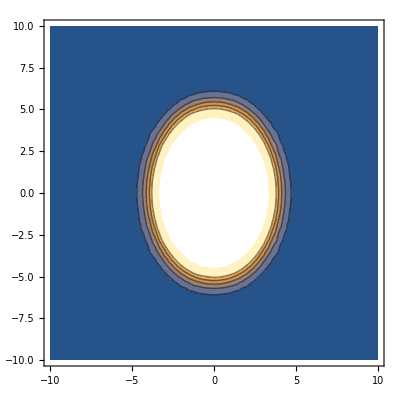

$Aborted

```mathematica
ContourPlot[tttInt[1][x,y],{x,-lim,lim},{y,-lim,lim}]
```